```mathematica
<<"/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/math.m"
```

```mathematica
pc=LibraryFunctionLoad[libhello,"get_pc",{},Integer];
```

```mathematica
nextpc=LibraryFunctionLoad[libhello,"next_pc",{},Integer];
```

```mathematica
pclist = Table[nextpc[],10000];
```

```mathematica
g=BlockMap[#[[1]]->#[[2]]&,pclist,2,1];
```

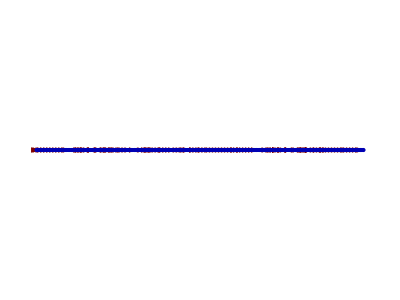

```mathematica
GraphPlot[Select[g,(#[[2]]-#[[1]])>6&],DirectedEdges-> True,Method->"LinearEmbedding"]
```

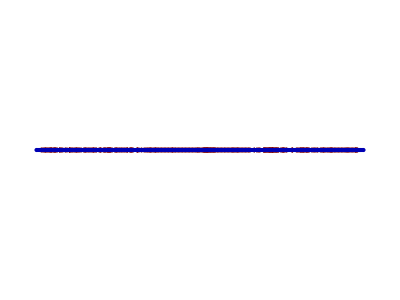

```mathematica
GraphPlot[g[[5000;;5500]],DirectedEdges-> True,Method->"LinearEmbedding"]
```